```mathematica
(*raw = Import["~/Downloads/optimizerHistory.json"];*)
raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"];
```

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

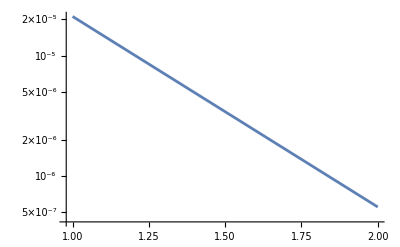

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
PlotRange->All,
Joined->True
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|L1PhaseSet→-20.,L2PhaseSet→-38.,Q1EkG→147.875,Q2EkG→-155.703,Q3EkG→113.077,Q4EkG→114.146,Q5EkG→-21.5835,Q6EkG→-126.27,S1ELkG→1364.45,S2ELkG→-3543.53,S3ELkG→-2100.16,S3ERkG→-533.42,S2ERkG→-2718.66,S1ERkG→838.776,PDrive_mean_x→-0.0000657505,PDrive_mean_y→-1.328×10^-7,PDrive_sigma_x→0.000200622,PDrive_sigma_y→0.0000448801,PDrive_xCost→0.000211121,PDrive_yCost→0.0000448803,PDrive_totalCost→0.000128001,PDrive_emitSI90_x→0.000473004,PDrive_emitSI90_y→0.0000327331,PDrive_zLen→0.0000282136,PDrive_zCentroid→991.332,PWitness_mean_x→-0.0000675947,PWitness_mean_y→-9.769×10^-7,PWitness_sigma_x→0.0000376608,PWitness_sigma_y→0.000110278,PWitness_xCost→0.0000773782,PWitness_yCost→0.000110282,PWitness_totalCost→0.0000938303,PWitness_emitSI90_x→0.0000235041,PWitness_emitSI90_y→0.0000234602,PWitness_zLen→8.8854×10^-6,PWitness_zCentroid→991.332,bunchSpacing→0.000136214,maximizeMe→0.0000211266|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

L1PhaseSet : -20.
L2PhaseSet : -38.
Q1EkG : 147.8747431031
Q2EkG : -155.7033712278
Q3EkG : 113.0766929733
Q4EkG : 114.145818373
Q5EkG : -21.5835472954
Q6EkG : -126.2699680599
S1ELkG : 1364.4533635026
S2ELkG : -3543.529706689
S3ELkG : -2100.1600778691
S3ERkG : -533.4195538336
S2ERkG : -2718.659205128
S1ERkG : 838.7757859812
PDrive_mean_x : -0.0000657505
PDrive_mean_y : -1.328e-7
PDrive_sigma_x : 0.0002006218
PDrive_sigma_y : 0.0000448801
PDrive_xCost : 0.0002111214
PDrive_yCost : 0.0000448803
PDrive_totalCost : 0.0001280009
PDrive_emitSI90_x : 0.0004730041
PDrive_emitSI90_y : 0.0000327331
PDrive_zLen : 0.0000282136
PDrive_zCentroid : 991.3316969865
PWitness_mean_x : -0.0000675947
PWitness_mean_y : -9.769e-7
PWitness_sigma_x : 0.0000376608
PWitness_sigma_y : 0.0001102781
PWitness_xCost : 0.0000773782
PWitness_yCost : 0.0001102824
PWitness_totalCost : 0.0000938303
PWitness_emitSI90_x : 0.0000235041
PWitness_emitSI90_y : 0.0000234602
PWitness_zLen : 8.8854e-6
PWitness_zCentroid : 991.3318332002
bunchSpacing : 0.0001362138
maximizeMe : 0.0000211266

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv